# Fisher estimates for a power law mass spectrum

```mathematica
SetDirectory@NotebookDirectory[];
<<MaTeX`
```

## No selection effects

## Inputs

```mathematica
$Assumptions={θ>0,θmax>0,θmin>0,θmax>θmin, σ>0 & σ<1000,λ>-1}
```

{θ>0,θmax>0,θmin>0,θmax>θmin,σ (σ>0&)<1000,λ>-1}

In this first example we do not consider selection effects, meaning we set the probability of detection for both source and population parameters to one.

```mathematica
pdetθ[M_]:=1
pdetλ[λ_]:=1
ppop[{θ_,θmin_,θmax_},λ_]:= λ/(θmax^λ-θmin^λ) θ^(λ-1)
```

We check here that the population model is correctly normalized.

```mathematica
Integrate[ppop[{θ,θmin,θmax},λ],{θ,θmin,θmax}]
```

1

A bunch of useful quantities that enter the Fisher matrix.

```mathematica
Γ = 1/σ^2;  (* True only in the case in which d = θ + noise. *)
Dmij= Γ ;  (* Only true in the absence of selection effects. *)
Dmi = D[pdetθ[θ],θ];
P = D[Log@ppop[{θ,θmin,θmax},λ],θ];
H = - D[D[Log@ppop[{θ,θmin,θmax},λ],θ],θ];
```

Choose the true parameters here.

```mathematica
λtrue =0.00001;
truepars ={Nobs->1000,λ->λtrue,σ->0.1,θmax->10^7, θmin->10^4}//N;
```

## Fisher matrix and precision estimates [simplified]

In this simplified scenario, we only consider the first (dominant) contribution to the Fisher matrix, without considering selection effects.
Notice that M is integrated out in the interval 10^4 M_0< M < 10^7 M_0.

```mathematica
SimpPopFisherNoSelectionEffects[λ_,{θ_,θmin_,θmax_},{i_,j_}]:=
Integrate[(1/ppop[{θ,θmin,θmax},λ])D[ppop[{θ,θmin,θmax},λ],i]*D[ppop[{θ,θmin,θmax},λ],j],{θ,θmin,θmax}]
```

```mathematica
ΓλλSimpNoSelectionEffects = SimpPopFisherNoSelectionEffects[λ,{M,10^4,10^7},{λ,λ}];//Timing
```

{13.1098,Null}

```mathematica
ΓλλSimpNoSelectionEffects
```

1/λ^2-(9 1000^λ Log[10]^2)/((-1+1000^λ)^2)

```mathematica
√(1/(Nobs*ΓλλSimpNoSelectionEffects))
Δα =%/.truepars
```

√(1/(Nobs (1/λ^2-(9 1000^λ Log[10]^2)/((-1+1000^λ)^2))))

0.0158814

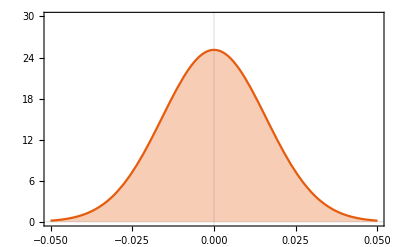

```mathematica
SimplifiedFisher=Plot[
PDF[NormalDistribution[λtrue,Δα],x]//Evaluate,{x,-.05,.05},
Filling->Axis,PlotRange->{All,{0,30}},
FrameLabel->{{MaTeX["\\text{PDF}",FontSize->17],None},{MaTeX["\\alpha_0",FontSize->17],None}},
FrameTicksStyle->Directive[Black,13],
TicksStyle->Directive[Black,AbsoluteThickness[100]],
PlotTheme-> "Scientific", 
Frame->True]
```

## Fisher matrix and precision estimates [including “higher orders”]

Notice that M is integrated out in the interval 10^4 M_0< M < 10^7 M_0.

```mathematica
PopFisherNoSelectionEffects[λ_,{θ_,θmin_,θmax_},{i_,j_}]:=(*TO FIX: issue in integration of higher orders. *)
Integrate[(1/ppop[{θ,θmin,θmax},λ])D[ppop[{θ,θmin,θmax},λ],i]*D[ppop[{θ,θmin,θmax},λ],j],{θ,10^4,10^7}] +1/2 Integrate[D[D[Log@(Γ+H),j],i]ppop[{θ,θmin,θmax},λ],{θ,10^4,10^7}]-1/2 Integrate[D[D[(Γ+H)^-1,j],i]Dmij ppop[{θ,θmin,θmax},λ],{θ,10^4,10^7}] - Integrate[D[D[P(Γ+H)^-1,j],i]Dmi ppop[{θ,θmin,θmax},λ],{θ,10^4,10^7}] -Integrate[D[D[P^2(Γ+H)^-1,j],i]*ppop[{θ,θmin,θmax},λ],{θ,10^4,10^7}]
```

```mathematica
(*Γλλfct = PopFisherNoSelectionEffects[λ,{M,10^4,10^7},{λ,λ}];//Timing (*Useful to debug*) *)
```

```mathematica
firstterm = Integrate[(pdetθ[θ]/(ppop[{θ,10^4,10^7},λ]*pdetλ[λ]))D[ppop[{θ,10^4,10^7},λ],λ]*D[ppop[{θ,10^4,10^7},λ],λ],{θ,10^4,10^7}];//Timing
```

{15.4624,Null}

```mathematica
secondterm  = - 1/pdetλ[λ]^2 D[pdetλ[λ],λ]*D[pdetλ[λ],λ];
```

```mathematica
thirdterm = 1/2 Integrate[D[D[Log@(Γ+H),λ],λ] pdetθ[θ]/pdetλ[λ] ppop[{θ,10^4,10^7},λ],{θ,10^4,10^7}];//Timing
```

{16.6586,Null}

```mathematica
fourthterm=-1/2 Integrate[D[D[(Γ+H)^-1,λ],λ]Dmij ppop[{θ,10^4,10^7},λ]/pdetλ[λ],{θ,10^4,10^7}];//Timing
```

{20.4833,Null}

```mathematica
fifthterm=- Integrate[D[D[P(Γ+H)^-1,λ],λ]Dmi ppop[{θ,10^4,10^7},λ]/pdetλ[λ],{θ,10^4,10^7}];
```

```mathematica
sixthterm=-Integrate[D[D[P^2(Γ+H)^-1,λ],λ] ppop[{θ,10^4,10^7},λ]/pdetλ[λ],{θ,10^4,10^7}];//Timing
```

{17.6735,Null}

```mathematica
Γλλ = firstterm +secondterm+thirdterm+fourthterm+fifthterm+sixthterm;
```

```mathematica
√(1/(Nobs*Γλλ))
%/.truepars
Δαfull=Re[%]
```

√(1/(Nobs (1/λ^2-1/(-1+1000^λ)2^(-2-4 λ) 625^-λ λ σ^4 ((10000^(-4+λ) (100000000 (-4+λ)-(-200000000+100000000 λ+2 σ^2-3 λ σ^2+λ^2 σ^2) Hypergeometric2F1[1,2-λ/2,3-λ/2,-((-1+λ) σ^2)/100000000]))/((-4+λ) (100000000+(-1+λ) σ^2))+(10^(7 (-4+λ)) (-100000000000000 (-4+λ)+(-200000000000000+100000000000000 λ+2 σ^2-3 λ σ^2+λ^2 σ^2) Hypergeometric2F1[1,2-λ/2,3-λ/2,-((-1+λ) σ^2)/100000000000000]))/((-4+λ) (100000000000000+(-1+λ) σ^2)))-1/((-1+1000^λ) (-1+λ)^3 (2+λ) σ^2)12500000 λ (((-2+λ+λ^2) σ^2 (λ^2 σ^2+4 (-50000000+σ^2)-5 λ (-20000000+σ^2)))/((100000000+(-1+λ) σ^2)^2)+1000^(2+λ) (-((-2+λ+λ^2) σ^2 (λ^2 σ^2+4 (-50000000000000+σ^2)-5 λ (-20000000000000+σ^2)))/((100000000000000+(-1+λ) σ^2)^2)+(-2+λ) λ Hypergeometric2F1[1,(2+λ)/2,(4+λ)/2,-100000000000000/((-1+λ) σ^2)])-(-2+λ) λ Hypergeometric2F1[1,(2+λ)/2,(4+λ)/2,-100000000/((-1+λ) σ^2)])-1/((-1+1000^λ) (-1+λ)^3 (4+λ) σ^4)2500000000000000 λ (((-4+3 λ+λ^2) σ^2 (2 σ^2+λ^2 σ^2+λ (100000000-3 σ^2)))/((100000000+(-1+λ) σ^2)^2)+1000^(4+λ) (-((-4+3 λ+λ^2) σ^2 (2 σ^2+λ^2 σ^2+λ (100000000000000-3 σ^2)))/((100000000000000+(-1+λ) σ^2)^2)+λ (2+λ) Hypergeometric2F1[1,(4+λ)/2,(6+λ)/2,-100000000000000/((-1+λ) σ^2)])-λ (2+λ) Hypergeometric2F1[1,(4+λ)/2,(6+λ)/2,-100000000/((-1+λ) σ^2)])-(9 1000^λ Log[10]^2)/((-1+1000^λ)^2))))

0.0158814+8.87709×10^-10 ⅈ

0.0158814

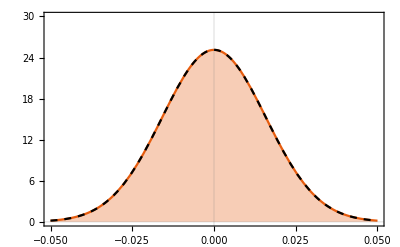

```mathematica
FullFisher = Plot[
PDF[NormalDistribution[λtrue,Δαfull],x]//Evaluate,{x,-.05,.05},
PlotStyle->{Black,Dashed}];
Show[SimplifiedFisher,FullFisher]
```

## With selection effects

## Generic case [to do]

```mathematica
(*PopFisher[λ_,{θ_,θmin_,θmax_},{i_,j_}]:=
Integrate[(pdetθ[θ]/(ppop[{θ,θmin,θmax},λ]*pdetλ[λ]))D[ppop[{θ,θmin,θmax},λ],i]*D[ppop[{θ,θmin,θmax},λ],j],{θ,10^4,10^7}]- 1/pdetλ[λ]^2 D[pdetλ[λ],i]*D[pdetλ[λ],j] +1/2 Integrate[D[D[Log@(Γ+H),j],i] pdetθ[θ]/pdetλ[λ] ppop[{θ,θmin,θmax},λ],{θ,10^4,10^7}]-1/2 Integrate[D[D[(Γ+H)^-1,j],i]Dmij ppop[{θ,θmin,θmax},λ]/pdetλ[λ],{θ,10^4,10^7}] - Integrate[D[D[P(Γ+H)^-1,j],i]Dmi ppop[{θ,θmin,θmax},λ]/pdetλ[λ],{θ,10^4,10^7}] -Integrate[D[D[P^2(Γ+H)^-1,j],i] ppop[{θ,θmin,θmax},λ]/pdetλ[λ],{θ,10^4,10^7}] *)
```